## 1. Baseline outputs for n^* and g_{10}^*

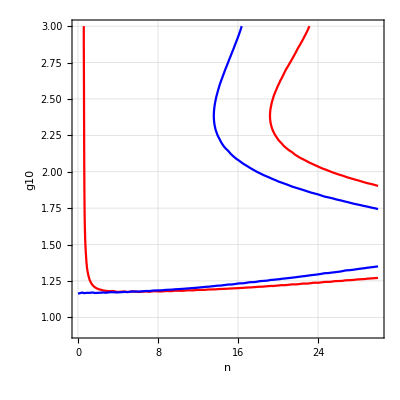

```mathematica
Clear[c0,cf,KK,h,phim,phif,lamdaf,beta,g10,g30,g12,n,dparital,CriticalCondition];

phim=1-phif;

c0=1;g30=1;cf=100;

g12=1;

h=0.01;beta=Pi/4;lamdaf=0.93;phif=0.8;KK=0.225;

CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;

dparital=D[CriticalCondition,n]//Simplify;

ContourPlot[{CriticalCondition==0,dparital==0},{n,0,30},{g10,0.9,3},ContourStyle->{Red,Blue},FrameLabel->{"n","g10"},GridLines->Automatic]
```

```mathematica
solution=FindRoot[{CriticalCondition==0,dparital==0},{{n,5},{g10,1.01}}]
g10mid=g10/. solution

nmid=n/. solution
```

{n→5.30715,g10→1.17459}

1.17459

5.30715

```mathematica
g10mid=1.1745935945603059;
nmid=5.307151031416191;

betaTarget=Pi/4;
lamdafTarget=0.93;
hTarget=0.01;
KKTarget=0.225;
phifTarget=0.8;
phim=1-phif;

c0=1;g30=1;cf=100;

g12=1;
```

## 2. Older_decrease n^* by 10% and increase g_{10}^* by 10%

### 2.1 w=0

#### 2.1.1 optimize : beta,lamdaf,h,KK,phif

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol];
g10mid=1.1745935945603059;
nmid=5.307151031416191;

betaTarget=Pi/4;
lamdafTarget=0.93;
hTarget=0.01;
KKTarget=0.225;
phifTarget=0.8;
phim=1-phif;

c0=1;g30=1;cf=100;

g12=1;

CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;

dparital=D[CriticalCondition,n]//Simplify;


g10=g10mid*1.1;
n=nmid*0.9;




w=0;

objective=(CriticalCondition^2+dparital^2)+w*(((h-hTarget)/hTarget)^2+((KK-KKTarget)/KKTarget)^2+((phif-phifTarget)/phifTarget)^2+((lamdaf-lamdafTarget)/lamdafTarget)^2+((beta-betaTarget)/betaTarget)^2);
{minResidual,bestSol}=NMinimize[{objective,0.7<=lamdaf<=1,0<=beta<=Pi/2, 0.001<=h<=0.015 , 0.1<=KK<= 0.3 ,0.55<=phif<= 0.85},{lamdaf,beta,h,KK,phif},Method->"DifferentialEvolution",MaxIterations->500];
v1h1=h/.  bestSol
v1KK1=KK/. bestSol
v1beta1=beta/. bestSol
v1lamdaf1=lamdaf/. bestSol
v1phif1=phif/. bestSol
```

0.015

0.1

1.08546

0.941029

0.55

#### 2.1.2 relative errors of n^* and g_{10}^*

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol,sol];



g10s=g10mid*1.1;
ns=nmid*0.9;


lamdaf=v1lamdaf1;
beta=v1beta1;
h=v1h1;
KK=v1KK1;
phif=v1phif1;


CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.15;
ninit=4.4;

sol=Quiet@FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8];

inverse1g101=g10/. sol;
inverse1n1=n/. sol;

err1g101=(inverse1g101-g10s)/g10s
err1n1=(inverse1n1-ns)/ns
```

-2.81841×10^-14

1.52284×10^-11

### 2.2 w=0.5

#### 2.2.1 optimize : beta,lamdaf,h,KK,phif

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol];

g10mid=1.1745935945603059;
nmid=5.307151031416191;

betaTarget=Pi/4;
lamdafTarget=0.93;
hTarget=0.01;
KKTarget=0.225;
phifTarget=0.8;
phim=1-phif;

c0=1;g30=1;cf=100;

g12=1;

CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;

dparital=D[CriticalCondition,n]//Simplify;


g10=g10mid*1.1;
n=nmid*0.9;

w=0.5;

objective=(CriticalCondition^2+dparital^2)+w*(((h-hTarget)/hTarget)^2+((KK-KKTarget)/KKTarget)^2+((phif-phifTarget)/phifTarget)^2+((lamdaf-lamdafTarget)/lamdafTarget)^2+((beta-betaTarget)/betaTarget)^2);
{minResidual,bestSol}=NMinimize[{objective,0.7<=lamdaf<=1,0<=beta<=Pi/2, 0.001<=h<=0.015 , 0.1<=KK<= 0.3 ,0.55<=phif<= 0.85},{lamdaf,beta,h,KK,phif},Method->"DifferentialEvolution",MaxIterations->500];
v1h2=h/.  bestSol
v1KK2=KK/. bestSol
v1beta2=beta/. bestSol
v1lamdaf2=lamdaf/. bestSol
v1phif2=phif/. bestSol
```

0.0108291

0.218158

0.728703

0.882267

0.821866

#### 2.2.2 relative errors of n^* and g_{10}^*

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol,sol];



g10s=g10mid*1.1;
ns=nmid*0.9;


lamdaf=v1lamdaf2;
beta=v1beta2;
h=v1h2;
KK=v1KK2;
phif=v1phif2;


CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.1576;
ninit=4.8699;

sol=Quiet@FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8];


inverse1g102=g10/. sol;
inverse1n2=n/. sol;

err1g102=(inverse1g102-g10s)/g10s
err1n2=(inverse1n2-ns)/ns
```

5.39389×10^-7

0.000247341

### 2.3 w=1

#### 2.3.1 optimize : beta,lamdaf,h,KK,phif

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol];

g10mid=1.1745935945603059;
nmid=5.307151031416191;

betaTarget=Pi/4;
lamdafTarget=0.93;
hTarget=0.01;
KKTarget=0.225;
phifTarget=0.8;
phim=1-phif;

c0=1;g30=1;cf=100;

g12=1;

CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;

dparital=D[CriticalCondition,n]//Simplify;


g10=g10mid*1.1;
n=nmid*0.9;


w=1;

objective=(CriticalCondition^2+dparital^2)+w*(((h-hTarget)/hTarget)^2+((KK-KKTarget)/KKTarget)^2+((phif-phifTarget)/phifTarget)^2+((lamdaf-lamdafTarget)/lamdafTarget)^2+((beta-betaTarget)/betaTarget)^2);
{minResidual,bestSol}=NMinimize[{objective,0.7<=lamdaf<=1,0<=beta<=Pi/2, 0.001<=h<=0.015 , 0.1<=KK<= 0.3 ,0.55<=phif<= 0.85},{lamdaf,beta,h,KK,phif},Method->"DifferentialEvolution",MaxIterations->500];
v1h3=h/.  bestSol
v1KK3=KK/. bestSol
v1beta3=beta/. bestSol
v1lamdaf3=lamdaf/. bestSol
v1phif3=phif/. bestSol
```

0.0108275

0.218168

0.728833

0.882295

0.821814

#### 2.3.2 relative errors of n^* and g_{10}^*

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol,sol];



g10s=g10mid*1.1;
ns=nmid*0.9;


lamdaf=v1lamdaf3;
beta=v1beta3;
h=v1h3;
KK=v1KK3;
phif=v1phif3;


CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.1576;
ninit=4.8699;

sol=Quiet@FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8];


inverse1g103=g10/. sol;
inverse1n3=n/. sol;

err1g103=(inverse1g103-g10s)/g10s
err1n3=(inverse1n3-ns)/ns
```

1.07588×10^-6

0.000494131

### 2.4 w=100

#### 2.4.1 optimize : beta,lamdaf,h,KK,phif

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol];

g10mid=1.1745935945603059;
nmid=5.307151031416191;

betaTarget=Pi/4;
lamdafTarget=0.93;
hTarget=0.01;
KKTarget=0.225;
phifTarget=0.8;
phim=1-phif;

c0=1;g30=1;cf=100;

g12=1;

CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;

dparital=D[CriticalCondition,n]//Simplify;


g10=g10mid*1.1;
n=nmid*0.9;


w=100;

objective=(CriticalCondition^2+dparital^2)+w*(((h-hTarget)/hTarget)^2+((KK-KKTarget)/KKTarget)^2+((phif-phifTarget)/phifTarget)^2+((lamdaf-lamdafTarget)/lamdafTarget)^2+((beta-betaTarget)/betaTarget)^2);
{minResidual,bestSol}=NMinimize[{objective,0.7<=lamdaf<=1,0<=beta<=Pi/2, 0.001<=h<=0.015 , 0.1<=KK<= 0.3 ,0.55<=phif<= 0.85},{lamdaf,beta,h,KK,phif},Method->"DifferentialEvolution",MaxIterations->500];
v1h3=h/.  bestSol
v1KK3=KK/. bestSol
v1beta3=beta/. bestSol
v1lamdaf3=lamdaf/. bestSol
v1phif3=phif/. bestSol
```

0.0105894

0.219774

0.748385

0.886502

0.814304

0.0108275

0.218168

0.728833

0.882295

0.821814

#### 2.3.2 relative errors of n^* and g_{10}^*

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol,sol];



g10s=g10mid*1.1;
ns=nmid*0.9;


lamdaf=v1lamdaf3;
beta=v1beta3;
h=v1h3;
KK=v1KK3;
phif=v1phif3;


CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.1576;
ninit=4.8699;

sol=Quiet@FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8];


inverse1g103=g10/. sol;
inverse1n3=n/. sol;

err1g103=(inverse1g103-g10s)/g10s
err1n3=(inverse1n3-ns)/ns
```

0.0000645703

0.0393021

### 2.5 w=100

#### 2.5.1 optimize : beta,lamdaf,h,KK,phif

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol];

g10mid=1.1745935945603059;
nmid=5.307151031416191;

betaTarget=Pi/4;
lamdafTarget=0.93;
hTarget=0.01;
KKTarget=0.225;
phifTarget=0.8;
phim=1-phif;

c0=1;g30=1;cf=100;

g12=1;

CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;

dparital=D[CriticalCondition,n]//Simplify;


g10=g10mid*1.1;
n=nmid*0.9;


w=1;

objective=(CriticalCondition^2+dparital^2)+w*(((h-hTarget)/hTarget)^2+((KK-KKTarget)/KKTarget)^2+((phif-phifTarget)/phifTarget)^2+((lamdaf-lamdafTarget)/lamdafTarget)^2)+1*((beta-betaTarget)/betaTarget)^2;
{minResidual,bestSol}=NMinimize[{objective,0.7<=lamdaf<=1,0<=beta<=Pi/2, 0.001<=h<=0.015 , 0.1<=KK<= 0.3 ,0.55<=phif<= 0.85},{lamdaf,beta,h,KK,phif},Method->"DifferentialEvolution",MaxIterations->500];
v1h3=h/.  bestSol;
v1KK3=KK/. bestSol;
v1beta3=beta/. bestSol;
v1lamdaf3=lamdaf/. bestSol;
v1phif3=phif/. bestSol;

Print[{v1h3,v1KK3,v1beta3,v1lamdaf3,v1phif3}]

Print[{(v1h3-hTarget)/hTarget,(v1KK3-KKTarget)/KKTarget,(v1beta3-betaTarget)/betaTarget,(v1lamdaf3-lamdafTarget)/lamdafTarget,(v1phif3-phifTarget)/phifTarget}]
```

{0.0108275,0.218168,0.728833,0.882295,0.821814}

{0.0827523,-0.0303656,-0.0720214,-0.0512957,0.0272671}

{0.0101717,0.223698,0.667768,0.868476,0.804737}

{0.0171654,-0.00578533,-0.149772,-0.0661553,0.00592066}

0.0103104

0.222621

0.675012

0.870138

0.808319

{0.0103104,0.222621,0.675012,0.870138,0.808319}

{0.0310399,-0.0105748,-0.140548,-0.0643679,0.0103981}

0.01

0.225

1.49164

0.93

0.8

0.013909

0.213889

0.868953

0.908966

0.612768

0.0134683

0.178974

0.90478

0.917606

0.685183

0.0108275

0.218168

0.728833

0.882295

0.821814

```mathematica
Pi/4.0
```

0.785398

#### 2.3.2 relative errors of n^* and g_{10}^*

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol,sol];



g10s=g10mid*1.1;
ns=nmid*0.9;


lamdaf=v1lamdaf3;
beta=v1beta3;
h=v1h3;
KK=v1KK3;
phif=v1phif3;


CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.1576;
ninit=4.8699;

sol=Quiet@FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8];


inverse1g103=g10/. sol;
inverse1n3=n/. sol;

err1g103=(inverse1g103-g10s)/g10s
err1n3=(inverse1n3-ns)/ns
```

0.0000645703

0.0393021

## 3. Older_decrease n^* by 20% and increase g_{10}^* by 20%

### 3.1 w=0

#### 3.1.1 optimize : beta,lamdaf,h,KK,phif

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol];


g10mid=1.1745935945603059;
nmid=5.307151031416191;

betaTarget=Pi/4;
lamdafTarget=0.93;
hTarget=0.01;
KKTarget=0.225;
phifTarget=0.8;
phim=1-phif;

c0=1;g30=1;cf=100;

g12=1;

CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;

dparital=D[CriticalCondition,n]//Simplify;


g10=g10mid*1.2;
n=nmid*0.8;


w=0;

objective=(CriticalCondition^2+dparital^2)+w*(((h-hTarget)/hTarget)^2+((KK-KKTarget)/KKTarget)^2+((phif-phifTarget)/phifTarget)^2+((lamdaf-lamdafTarget)/lamdafTarget)^2+((beta-betaTarget)/betaTarget)^2);
{minResidual,bestSol}=NMinimize[{objective,0.7<=lamdaf<=1,0<=beta<=Pi/2, 0.001<=h<=0.015 , 0.1<=KK<= 0.3 ,0.55<=phif<= 0.85},{lamdaf,beta,h,KK,phif},Method->"DifferentialEvolution",MaxIterations->500];
v2h1=h/.  bestSol
v2KK1=KK/. bestSol
v2beta1=beta/. bestSol
v2lamdaf1=lamdaf/. bestSol
v2phif1=phif/. bestSol
```

0.015

0.1

1.00077

0.905844

0.55

#### 3.1.2 relative errors of n^* and g_{10}^*

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol,sol];



g10s=g10mid*1.2;
ns=nmid*0.8;


lamdaf=v2lamdaf1;
beta=v2beta1;
h=v2h1;
KK=v2KK1;
phif=v2phif1;


CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.26285210108347;
ninit=4.328851728149631;

sol=Quiet@FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8];

inverse2g101=g10/. sol;
inverse2n1=n/. sol;

err2g101=(inverse2g101-g10s)/g10s
err2n1=(inverse2n1-ns)/ns
```

-1.88866×10^-12

4.86407×10^-11

### 3.2 w=0.5

#### 3.2.1 optimize : beta,lamdaf,h,KK,phif

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol];
g10mid=1.1745935945603059;
nmid=5.307151031416191;

betaTarget=Pi/4;
lamdafTarget=0.93;
hTarget=0.01;
KKTarget=0.225;
phifTarget=0.8;
phim=1-phif;

c0=1;g30=1;cf=100;

g12=1;

CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;

dparital=D[CriticalCondition,n]//Simplify;


g10=g10mid*1.2;
n=nmid*0.8;

w=0.5;

objective=(CriticalCondition^2+dparital^2)+w*(((h-hTarget)/hTarget)^2+((KK-KKTarget)/KKTarget)^2+((phif-phifTarget)/phifTarget)^2+((lamdaf-lamdafTarget)/lamdafTarget)^2+((beta-betaTarget)/betaTarget)^2);
{minResidual,bestSol}=NMinimize[{objective,0.7<=lamdaf<=1,0<=beta<=Pi/2, 0.001<=h<=0.015 , 0.1<=KK<= 0.3 ,0.55<=phif<= 0.85},{lamdaf,beta,h,KK,phif},Method->"DifferentialEvolution",MaxIterations->500];
v2h2=h/.  bestSol
v2KK2=KK/. bestSol
v2beta2=beta/. bestSol
v2lamdaf2=lamdaf/. bestSol
v2phif2=phif/. bestSol
```

0.0118344

0.20762

0.66818

0.833705

0.85

#### 3.2.2 relative errors of n^* and g_{10}^*

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol,sol];



g10s=g10mid*1.2;
ns=nmid*0.8;


lamdaf=v2lamdaf2;
beta=v2beta2;
h=v2h2;
KK=v2KK2;
phif=v2phif2;


CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.26285210108347;
ninit=4.328851728149631;

sol=Quiet@FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8];


inverse2g102=g10/. sol;
inverse2n2=n/. sol;

err2g102=(inverse2g102-g10s)/g10s
err2n2=(inverse2n2-ns)/ns
```

1.88411×10^-6

0.000649646

### 3.3 w=1

#### 3.3.1 optimize : beta,lamdaf,h,KK,phif

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol];

g10mid=1.1745935945603059;
nmid=5.307151031416191;

betaTarget=Pi/4;
lamdafTarget=0.93;
hTarget=0.01;
KKTarget=0.225;
phifTarget=0.8;
phim=1-phif;

c0=1;g30=1;cf=100;

g12=1;

CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;

dparital=D[CriticalCondition,n]//Simplify;


g10=g10mid*1.2;
n=nmid*0.8;

w=1;

objective=(CriticalCondition^2+dparital^2)+w*(((h-hTarget)/hTarget)^2+((KK-KKTarget)/KKTarget)^2+((phif-phifTarget)/phifTarget)^2+((lamdaf-lamdafTarget)/lamdafTarget)^2+((beta-betaTarget)/betaTarget)^2);
{minResidual,bestSol}=NMinimize[{objective,0.7<=lamdaf<=1,0<=beta<=Pi/2, 0.001<=h<=0.015 , 0.1<=KK<= 0.3 ,0.55<=phif<= 0.85},{lamdaf,beta,h,KK,phif},Method->"DifferentialEvolution",MaxIterations->500];
v2h3=h/.  bestSol
v2KK3=KK/. bestSol
v2beta3=beta/. bestSol
v2lamdaf3=lamdaf/. bestSol
v2phif3=phif/. bestSol
```

0.011545

0.210734

0.634683

0.823944

0.838833

#### 3.3.2 relative errors of n^* and g_{10}^*

```mathematica
Clear[lamdaf,beta,h,KK,phif,g10,n,dparital,CriticalCondition,w,minResidual,bestSol,sol];



g10s=g10mid*1.2;
ns=nmid*0.8;


lamdaf=v2lamdaf3;
beta=v2beta3;
h=v2h3;
KK=v2KK3;
phif=v2phif3;


CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.26285210108347;
ninit=4.328851728149631;

sol=Quiet@FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8];


inverse2g103=g10/. sol;
inverse2n3=n/. sol;

err2g103=(inverse2g103-g10s)/g10s
err2n3=(inverse2n3-ns)/ns
```

2.82386×10^-6

0.000993372

## 4. Design Efforts

### 4.1 The designed parameters

10 % : w = 0 :

```mathematica
Clear[h,K,beta,lamdaf,phif,error10,errorn];
Clear["Global`*"];
```

```mathematica
h[1]=0.014999999848022675;
K[1]=0.10000000304044296;
beta[1]=1.0854635803233892;
lamdaf[1]=0.9410293891182054;
phif[1]=0.5500000453660889;


errorg10[1]=-2.8184073334230156*^-14;
errorn[1]=1.522837797336836*^-11;


ToString[NumberForm[100*(-0.1+0.9*errorg10[1]),{Infinity,2}]]<>"%"

ToString[NumberForm[100*(-0.1+0.9*errorn[1]),{Infinity,2}]]<>"%"
```

-10.00%

-10.00%

10 % : w = 0.5 :

```mathematica
h[2]=0.010829069125430166;
K[2]=0.21815833086953418;
beta[2]=0.728702559106058;
lamdaf[2]=0.8822670114048208;
phif[2]=0.8218660736292487;


errorg10[2]=5.393892847772178*^-7;
errorn[2]=0.000247341205969709;


ToString[NumberForm[100*(-0.1+0.9*errorg10[2]),{Infinity,1}]]<>"%"

ToString[NumberForm[100*(-0.1+0.9*errorn[2]),{Infinity,1}]]<>"%"
```

-10.0%

-10.0%

10 % : w = 1 :

```mathematica
h[3]=0.010827523135692022;
K[3]=0.21816773886402596;
beta[3]=0.7288326959121649;
lamdaf[3]=0.8822949897020044;
phif[3]=0.8218136504467534;


errorg10[3]=1.0758842693856877*^-6;
errorn[3]=0.0004941314600853111;





ToString[NumberForm[100*(-0.1+0.9*errorg10[3]),{Infinity,1}]]<>"%"

ToString[NumberForm[100*(-0.1+0.9*errorn[3]),{Infinity,1}]]<>"%"
```

-10.0%

-10.0%

20%:w=0:

```mathematica
h[4]=0.014999999999546348;
K[4]=0.10000000000888551;
beta[4]=1.0007653816677327;
lamdaf[4]=0.9058439336374141;
phif[4]=0.5500000001699303;


errorg10[4]=-1.8886623004293393*^-12;
errorn[4]=4.864069347991285*^-11;

ToString[NumberForm[100*(-0.2+0.8*errorg10[4]),{Infinity,1}]]<>"%"

ToString[NumberForm[100*(-0.2+0.8*errorn[4]),{Infinity,1}]]<>"%"
```

-20.0%

-20.0%

20%: w=0.5:

```mathematica
h[5]=0.01183435411551903;
K[5]=0.2076198806559442;
beta[5]=0.6681804025136894;
lamdaf[5]=0.8337048924069991;
phif[5]=0.8499999243362716;


errorg10[5]=1.8841145857659007*^-6;
errorn[5]=0.0006496457651425725;

ToString[NumberForm[100*(-0.2+0.8*errorg10[5]),{Infinity,1}]]<>"%"

ToString[NumberForm[100*(-0.2+0.8*errorn[5]),{Infinity,1}]]<>"%"
```

-20.0%

-19.9%

20%: w=1:

```mathematica
h[6]=0.011545030931362504;
K[6]=0.21073373995396966;
beta[6]=0.6346833799550365;
lamdaf[6]=0.8239437205724708;
phif[6]=0.8388328818421492;


errorg10[6]=2.8238569597287376*^-6;
errorn[6]=0.0009933720095390236;




ToString[NumberForm[100*(-0.2+0.8*errorg10[6]),{Infinity,1}]]<>"%"

ToString[NumberForm[100*(-0.2+0.8*errorn[6]),{Infinity,1}]]<>"%"
```

-20.0%

-19.9%

### 4.2 Relative change (design efforts)

```mathematica
betaTarget=Pi/4;
lamdafTarget=0.93;
hTarget=0.01;
KKTarget=0.225; 
phifTarget=0.8;






Table[{NumberForm[h[i],2], NumberForm[K[i],2],NumberForm[beta[i],2],NumberForm[lamdaf[i],2],NumberForm[phif[i],2]},{i,1,6}]//MatrixForm

Table[{(h[i]-hTarget)/hTarget, (K[i]-KKTarget)/KKTarget,(beta[i]-betaTarget)/betaTarget,(lamdaf[i]-lamdafTarget)/lamdafTarget,(phif[i]-phifTarget)/phifTarget},{i,1,6}]//MatrixForm;


(*Table[{ToString[NumberForm[100*(h[i]-hTarget)/hTarget,{Infinity,2}]]<>"%", ToString[NumberForm[100*(K[i]-KKTarget)/KKTarget,{Infinity,2}]]<>"%",ToString[NumberForm[100*(beta[i]-betaTarget)/betaTarget,{Infinity,2}]]<>"%",ToString[NumberForm[100*(lamdaf[i]-lamdafTarget)/lamdafTarget,{Infinity,2}]]<>"%",ToString[NumberForm[100*(phif[i]-phifTarget)/phifTarget,{Infinity,2}]]<>"%"},{i,1,6}]//MatrixForm



Table[{ToString[NumberForm[100*(h[i]-hTarget)/hTarget,{Infinity,1}]]<>"%", ToString[NumberForm[100*(K[i]-KKTarget)/KKTarget,{Infinity,1}]]<>"%",ToString[NumberForm[100*(beta[i]-betaTarget)/betaTarget,{Infinity,1}]]<>"%",ToString[NumberForm[100*(lamdaf[i]-lamdafTarget)/lamdafTarget,{Infinity,1}]]<>"%",ToString[NumberForm[100*(phif[i]-phifTarget)/phifTarget,{Infinity,1}]]<>"%"},{i,1,6}]//MatrixForm*)



Table[{NumberForm[100*(h[i]-hTarget)/hTarget,{Infinity,1}], NumberForm[100*(K[i]-KKTarget)/KKTarget,{Infinity,1}],NumberForm[100*(beta[i]-betaTarget)/betaTarget,{Infinity,1}],NumberForm[100*(lamdaf[i]-lamdafTarget)/lamdafTarget,{Infinity,1}],NumberForm[100*(phif[i]-phifTarget)/phifTarget,{Infinity,1}]},{i,1,6}]//MatrixForm
```

(0.015 | 0.1 | 1.1 | 0.94 | 0.55
0.011 | 0.22 | 0.73 | 0.88 | 0.82
0.011 | 0.22 | 0.73 | 0.88 | 0.82
0.015 | 0.1 | 1. | 0.91 | 0.55
0.012 | 0.21 | 0.67 | 0.83 | 0.85
0.012 | 0.21 | 0.63 | 0.82 | 0.84)

(50.0 | -55.6 | 38.2 | 1.2 | -31.2
8.3 | -3.0 | -7.2 | -5.1 | 2.7
8.3 | -3.0 | -7.2 | -5.1 | 2.7
50.0 | -55.6 | 27.4 | -2.6 | -31.2
18.3 | -7.7 | -14.9 | -10.4 | 6.2
15.5 | -6.3 | -19.2 | -11.4 | 4.9)